-Graphics-
-Graphics-

(Bienvenidos a eScience - Estadistica!
https://github.com/josemramirez/mmaescience/statistics -[for Statistical M.])_beta^v14

# Statistical Mechanics - Lec. 10 III.G Conservation Laws

```mathematica
(*-------------------------------------*)
t1=TimeObject[{7,0,0}];
t2=TimeObject[{7,10,0}];
Lab1="Thermo.&Stat.\nGeneral Picture";
(*-------------------------------------*)
(*-------------------------------------*)
t3=TimeObject[{7,8,0}];
t4=TimeObject[{7,30,0}];
Lab2="Thermo.&Stat.\nMindMap Lecture";
(*-------------------------------------*)
(*-------------------------------------*)
t5=TimeObject[{8,2,0}];
t6=TimeObject[{8,20,0}];
Lab3="Thermo.&Stat.\nStudents talks";
(*-------------------------------------*)
(*-------------------------------------*)
t71=TimeObject[{8,5,0}];
t81=TimeObject[{8,10,0}];
Lab41="Thermo.&Stat.\nBreak";
(*-------------------------------------*)
(*-------------------------------------*)
t7=TimeObject[{7,35,0}];
t8=TimeObject[{8,45,0}];
Lab4="Thermo.&Stat.\nSlides";
(*-------------------------------------*)
(*-------------------------------------*)
(*-------------------------------------*)
(*-------------------------------------*)
t72=TimeObject[{8,50,0}];
t82=TimeObject[{9,0,0}];
Lab42=Hyperlink[Style["Thermo.&Stat.\n   Questions?\n   &\n   Chat..."],"https://mmaitex-gemmini.fly.dev/"];

TS1=TimelinePlot[{
Interval[{t1,t2}]->Lab1,
Interval[{t3,t4}]->Lab2,
Interval[{t5,t6}]->Lab3,
Interval[{t71,t81}]->Lab41,
Interval[{t7,t8}]->Lab4,
Interval[{t72,t82}]->Lab42
},
Frame->True,
FrameStyle->Directive[Thickness[0.003],FontFamily->"Comic Sans MS", FontSize->28],
LabelStyle->Directive[FontFamily->"Comic Sans MS",Black,18],ImageSize->800,Background->LightBlue,AspectRatio->0.35
]
```

-Graphics-

## Approach to equilibrium

(1) -- Let's talk about how a gas gets back to balance when we mess with it. Imagine we shake up a gas that was sitting quietly in equilibrium. Now, we want to know how it settles down again. This doesn't happen all at once – there are different steps that take different amounts of time. It's like a bunch of dominoes falling one after another, each step leading to the next until the gas is calm again. Understanding these steps helps us see how nature brings things back to order.

(2) -- In a gas, the quickest events are collisions between pairs of nearby particles. These happen very rapidly, in a timeframe we call τc. After these collisions, the probability of finding two particles at positions q1 and q2 becomes equal to the product of the probabilities of finding each particle independently at those positions. This is true when the particles are far apart compared to their size. The same principle applies to groups of three or more particles. This process, where complex probabilities simplify into products of simpler ones, is called relaxation.

```mathematica
(3) -- In the next step, our distribution function f₁ settles into a local equilibrium state. This happens over a timeframe called the mean free time, denoted by τ×. The mean free time is the natural timescale set by particle collisions in our system. After this brief period, the quantities that don't change during collisions (like mass, energy, and momentum) reach a state of local equilibrium. We can then define a local density at each point in our system by adding up the contributions from particles with all possible momenta. This local density will change over time as our system evolves.
```

Statistical Mechanics
Ramirez (4)

```mathematica
MaTeX["n(\\vec{q}, t)=\\int f_{1}(\\vec{p}, \\vec{q}, t)\\,  d \\vec{p} ", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["n(\\vec{q}, t)=\\int f_{1}(\\vec{p}, \\vec{q}, t)\\,  d \\vec{p} ",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

n[q⃗,t]==∫f_1[p⃗,q⃗,t]ⅆ p⃗

```mathematica
(5) -- as well as a local expectation value for any operator
```

```mathematica
MaTeX["\\mathcal{O}(\\vec{p}, \\vec{q}, t)",Magnification->5]
```

-Graphics-

Statistical Mechanics
Ramirez (6)

```mathematica
MaTeX["\\langle\\mathcal{O}(\\vec{q}, t)\\rangle=\\frac{1}{n(\\vec{q}, t)} \\int f_{1}(\\vec{p}, \\vec{q}, t) \\mathcal{O}(\\vec{p}, \\vec{q}, t)\\,  d^3 \\vec{p} ", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\langle\\mathcal{O}(\\vec{q}, t)\\rangle=\\frac{1}{n(\\vec{q}, t)} \\int f_{1}(\\vec{p}, \\vec{q}, t) \\mathcal{O}(\\vec{p}, \\vec{q}, t)\\,  d \\vec{p} ",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

⟨O[q⃗,t]⟩==(∫f_1[p⃗,q⃗,t] O[p⃗,q⃗,t]ⅆ p⃗)/n[q⃗,t]

(7) -- After a system experiences a disturbance, it goes through different stages of relaxation. First, the densities and average values of various properties settle into a local equilibrium. This happens quickly, over short time scales we call τc and τx.

Then, a slower process begins. The system gradually moves towards a global equilibrium. This takes more time and involves larger areas of the system. We describe this final stage using the Boltzmann equation, focusing on how conserved quantities (like mass, energy, or momentum) change over time.

To make things easier, we use hydrodynamic equations to track these changes. These equations help us understand how the system as a whole reaches its final, stable state.

```mathematica
(8) -- In our study of two-body collisions, we encounter special quantities that remain constant throughout the interaction. We call these "conserved quantities." They don't change before, during, or after the collision. Examples include total energy, momentum, and angular momentum. These conserved quantities obey specific mathematical relationships that we'll explore in detail later. Understanding these conserved quantities is crucial for predicting the outcomes of collisions and analyzing the behavior of particle systems.
```

Statistical Mechanics
Ramirez (9)

```mathematica
MaTeX["\\chi\\left(\\vec{p}_{1}, \\vec{q}, t\\right)+\\chi\\left(\\vec{p}_{2}, \\vec{q}, t\\right)=\\chi\\left(\\vec{p}_{1}^{\\prime}, \\vec{q}, t\\right)+\\chi\\left(\\vec{p}_{2}^{\\prime}, \\vec{q}, t\\right)", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\chi\\left(\\vec{p}_{1}, \\vec{q}, t\\right)+\\chi\\left(\\vec{p}_{2}, \\vec{q}, t\\right)=\\chi\\left(\\vec{p}_{1}^{\\prime}, \\vec{q}, t\\right)+\\chi\\left(\\vec{p}_{2}^{\\prime}, \\vec{q}, t\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

χ[(p⃗)_1,q⃗,t]+χ[(p⃗)_2,q⃗,t]==χ[(p⃗)_1',q⃗,t]+χ[(p⃗)_2',q⃗,t]

```mathematica
(10) -- In a collision between two particles, we denote their initial momenta as p₁ and p₂, and their final momenta as p₁' and p₂'. Conservation of momentum requires that the total momentum before the collision equals the total momentum after:

p₁ + p₂ = p₁' + p₂'

This fundamental principle ensures that momentum is neither created nor destroyed during the collision process, maintaining the overall balance of motion in the system.
```

Statistical Mechanics
Ramirez (11)

```mathematica
MaTeX["J_{\\chi}(\\vec{q}, t)=\\left.\\int \\chi(\\vec{p}, \\vec{q}, t) \\frac{d f_{1}}{d t}\\right|_{\\text {coll.}}(\\vec{p}, \\vec{q}, t) \\,  d^3 \\vec{p} =0", Magnification -> 4]
```

-Graphics-

## Proof: Using the form of the collision integral

```mathematica
(12) -- When particles collide, they exchange energy and momentum. The collision integral helps us understand how these collisions affect the overall behavior of a system. It's like keeping track of all the bumper car collisions in an amusement park and figuring out how they change the overall movement of all the cars.

To prove our point, we'll use the collision integral's formula. This formula considers how often particles collide, their speeds before and after collisions, and how these collisions change the distribution of particles in the system.
```

Statistical Mechanics
Ramirez (13)

```mathematica
MaTeX["J_{\\chi}=-\\int d^3\\vec{p}_{1}d^3\\vec{p}_{2} d^2\\vec{b}\\left|\\vec{v}_{1}-\\vec{v}_{2}\\right|\\left[f_{1}\\left(\\vec{p}_{1}\\right) f_{1}\\left(\\vec{p}_{2}\\right)-f_{1}\\left(\\vec{p}_{1}^{\\prime}\\right) f_{1}\\left(\\vec{p}_{2}^{\\prime}\\right)\\right] [\\chi\\left(\\vec{p}_{1}\\right)+\\chi\\left(\\vec{p}_{2}\\right)]", Magnification -> 4]
```

-Graphics-

(14) -- Let's simplify this concept a bit. When we're working with these equations, we often have multiple particles to consider. To make our calculations easier, we can swap the labels of two particles, say particle 1 and particle 2. This doesn't change the physics of the system, but it can simplify our math.

We do this swapping and then take an average. This technique is particularly useful when we're proving the H-theorem, which is an important concept in statistical mechanics.

By doing this swap and average, we're essentially treating the particles as indistinguishable. This is a key idea in statistical mechanics, where we're often more interested in the overall behavior of a system rather than the specific details of individual particles.

Remember, in real systems, we're dealing with enormous numbers of particles. This swapping and averaging technique helps us manage that complexity and extract meaningful results.

Statistical Mechanics
Ramirez (15)

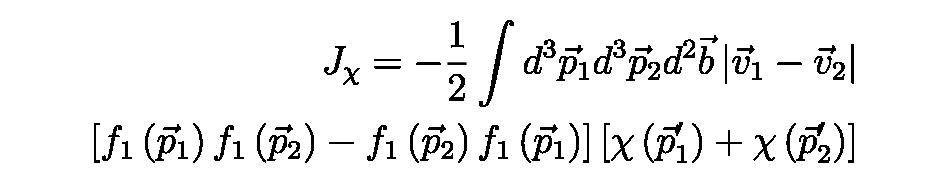

```mathematica
MaTeX["\\begin{aligned} J_{\\chi}=-\\frac{1}{2} \\int d^3\\vec{p}_{1}d^3\\vec{p}_{2} d^2\\vec{b} \\left|\\vec{v}_{1}-\\vec{v}_{2}\\right| \\\\ \\left[f_{1}\\left(\\vec{p}_{1}\\right) f_{1}\\left(\\vec{p}_{2}\\right) - f_{1}\\left(\\vec{p}_{2}\\right) f_{1}\\left(\\vec{p}_{1}\\right)\\right] \\left[ \\chi\\left(\\vec{p}_{1}^{\\prime}\\right) + \\chi \\left(\\vec{p}_{2}^{\\prime}\\right) \\right]  \\end{aligned}", Magnification -> 4]
```

```mathematica
(16) -- Let's look at this from a different angle. Instead of focusing on what we start with (the p1, p2, and b vectors), we'll shift our attention to what we end up with after the collision (p1', p2', and b' vectors). 

Think of it like this: we're changing our perspective from before the collision to after it. When we do this and adjust our math accordingly, the equation we were working with takes on a new form.

This switch in viewpoint helps us see the problem in a fresh light, often making it easier to solve or understand. It's a bit like looking at a building from the back instead of the front - same building, but you might notice different details.
```

Statistical Mechanics
Ramirez (17)

```mathematica
MaTeX["J_{\\chi}=-\\frac{1}{2} \\int d^3\\vec{p}_{1}d^3\\vec{p}_{2} d^2\\vec{b}\\left|\\vec{v}_{1}-\\vec{v}_{2}\\right|\\left[f_{1}\\left(\\vec{p}_{1}^{\\prime}\\right) f_{1}\\left(\\vec{p}_{2}^{\\prime}\\right)-f_{1}\\left(\\vec{p}_{1}\\right) f_{1}\\left(\\vec{p}_{2}\\right)\\right]\\left[\\chi\\left(\\vec{p}_{1}^{\\prime}\\right)+\\chi\\left(\\vec{p}_{2}^{\\prime}\\right)\\right]", Magnification -> 4]
```

-Graphics-

```mathematica
(18) -- Averaging the last two equations leads to
```

Statistical Mechanics
Ramirez (19)

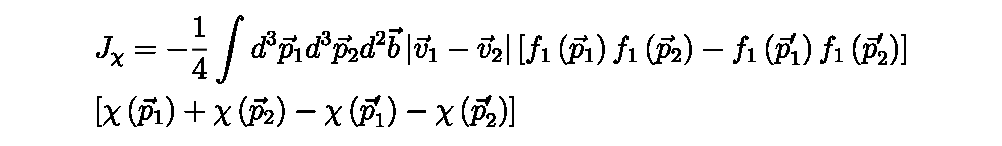

```mathematica
MaTeX["\\begin{aligned}& J_{\\chi}=-\\frac{1}{4} \\int d^{3} \\vec{p}_{1} d^{3} \\vec{p}_{2} d^{2} \\vec{b}\\left|\\vec{v}_{1}-\\vec{v}_{2}\\right| {\\left[f_{1}\\left(\\vec{p}_{1}\\right) f_{1}\\left(\\vec{p}_{2}\\right)-f_{1}\\left(\\vec{p}_{1}^{\\prime}\\right) f_{1}\\left(\\vec{p}_{2}^{\\prime}\\right)\\right]} \\\\& {\\left[\\chi\\left(\\vec{p}_{1}\\right)+\\chi\\left(\\vec{p}_{2}\\right)-\\chi\\left(\\vec{p}_{1}^{\\prime}\\right)-\\chi\\left(\\vec{p}_{2}^{\\prime}\\right)\\right]}\\end{aligned}", Magnification -> 4]
```

(20) -- In our exploration of thermodynamics, we've encountered a fascinating result. Remember equation (III.71)? It showed us that a certain quantity equals zero. This might seem simple, but it has profound implications for how we understand energy and its behavior in systems. 

Think of it like this: when we observe a system at equilibrium, there's a delicate balance at play. This zero result tells us that, in this balanced state, there's no net flow of energy or matter. It's a bit like a perfectly level see-saw – everything is still and steady.

This concept is crucial for predicting how systems will behave and helps us design more efficient machines and processes. As you continue your studies, you'll see how this principle underpins many aspects of thermodynamics and statistical mechanics.

(21) -- Okay, let's dive into what happens when we look at how the average values of χ change over time. We can replace the collision term in equation (III.72) with the streaming terms from the left side of the Boltzmann equation. This gives us a new way to understand how these average values evolve. By doing this, we're connecting the microscopic behavior of particles to the overall changes we see in the system. This approach helps us bridge the gap between individual particle interactions and the broader thermodynamic properties we observe.

Statistical Mechanics
Ramirez (22)

```mathematica
MaTeX["J_{\\chi}(\\vec{q}, t)=\\int \\chi(\\vec{p}, \\vec{q}, t)\\left[\\partial_{t}+\\frac{p_{\\alpha}}{m} \\partial_{\\alpha}+F_{\\alpha} \\frac{\\partial}{\\partial p_{\\alpha}}\\right] f_{1}(\\vec{p}, \\vec{q}, t) \\,  d^3 \\vec{p} =0", Magnification -> 4]
```

-Graphics-

(23) -- In our study of thermodynamics and statistical mechanics, we often use shorthand notations to make our equations more compact and easier to read. Let's introduce a few of these:

∂t means we're taking a partial derivative with respect to time.
∂α means we're taking a partial derivative with respect to a generalized coordinate qα.
Fα = -∂U/∂qα represents the generalized force associated with the coordinate qα.

These notations help us write complex equations more simply. We'll use them to rewrite our main equation in a more manageable form. Remember, these are just tools to help us express physical concepts more efficiently.

Statistical Mechanics
Ramirez (24)

```mathematica
MaTeX["\\int \\left\\{\\left[\\partial_{t}+\\frac{p_{\\alpha}}{m} \\partial_{\\alpha}+F_{\\alpha} \\frac{\\partial}{\\partial p_{\\alpha}}\\right]\\left(\\chi f_{1}\\right)-f_{1}\\left[\\partial_{t}+\\frac{p_{\\alpha}}{m} \\partial_{\\alpha}+F_{\\alpha} \\frac{\\partial}{\\partial p_{\\alpha}}\\right] \\chi\\right\\}   d^3 \\vec{p}=0", Magnification -> 4]
```

-Graphics-

(25) -- In our thermodynamic system, we can ignore the third term because it's a complete derivative, which means it doesn't contribute to our overall calculation. Now, let's focus on the other terms. Remember how we defined expectation values earlier? We can use that definition to rearrange the remaining terms into a more useful form.

Think of it like organizing puzzle pieces. We're taking the pieces we have (our terms) and putting them together in a way that makes more sense for solving our thermodynamic problem. This rearrangement helps us see the physical meaning more clearly without getting lost in complex mathematics.

Statistical Mechanics
Ramirez (26)

```mathematica
MaTeX["\\partial_{t}(n\\langle\\chi\\rangle)+\\partial_{\\alpha}\\left(n\\left\\langle\\frac{p_{\\alpha}}{m} \\chi\\right\\rangle\\right)-n\\left\\langle\\partial_{t} \\chi\\right\\rangle-n\\left\\langle\\frac{p_{\\alpha}}{m} \\partial_{\\alpha} \\chi\\right\\rangle-n F_{\\alpha}\\left\\langle\\frac{\\partial \\chi}{\\partial p_{\\alpha}}\\right\\rangle=0", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\partial_{t}(n\\langle\\chi\\rangle)+\\partial_{\\alpha}\\left(n\\left\\langle\\frac{p_{\\alpha}}{m} \\chi\\right\\rangle\\right)-n\\left\\langle\\partial_{t} \\chi\\right\\rangle-n\\left\\langle\\frac{p_{\\alpha}}{m} \\partial_{\\alpha} \\chi\\right\\rangle-n F_{\\alpha}\\left\\langle\\frac{\\partial \\chi}{\\partial p_{\\alpha}}\\right\\rangle=0",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

∂_t (n ⟨χ⟩)+∂_α (n ⟨(p_α χ)/m⟩)-n ⟨∂_t χ⟩-n ⟨(p_α ∂_α χ)/m⟩-n F_α ⟨∂_{p_α} χ⟩==0

```mathematica
(27) -- In our study of elastic collisions, we've identified five key quantities that remain constant: the number of particles, the three components of momentum, and kinetic energy. These conserved quantities are crucial in understanding the behavior of particles during collisions.

For each of these conserved quantities, we can develop a corresponding hydrodynamic equation. These equations help us describe the flow and behavior of fluids or gases at a macroscopic level, based on the conservation principles we've observed at the microscopic level.

In the following sections, we'll construct these hydrodynamic equations, which will provide us with a powerful tool for analyzing and predicting the behavior of systems involving many particles undergoing elastic collisions.
```

## (a) Particle number:

```mathematica
(28) -- Let's consider what happens when we set χ equal to 1 in our equation. This simplifies our expression and gives us a direct way to calculate the particle number. Imagine you have a box filled with tiny particles, like atoms or molecules. By using this simplified equation, we can figure out how many of these particles are inside the box. It's a bit like counting marbles in a jar, but we're using math to do it instead of counting one by one. This is really useful when we're dealing with systems that have a huge number of particles, which is often the case in thermodynamics and statistical mechanics.
```

Statistical Mechanics
Ramirez (29)

```mathematica
MaTeX["\\partial_{t} n+\\partial_{\\alpha}\\left(n u_{\\alpha}\\right)=0", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\partial_{t} n+\\partial_{\\alpha}\\left(n u_{\\alpha}\\right)=0",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

∂_t n+∂_α (n u_α)==0

(30) -- In our study of fluid dynamics, we encounter the concept of local velocity. This is the velocity of a fluid at a specific point in space and time. We denote it as v(r,t), where r represents the position vector and t is time. 

The local velocity is crucial for understanding fluid behavior. It tells us how fast and in which direction the fluid is moving at any given location. This concept is fundamental to analyzing fluid flow patterns, pressure distributions, and other important phenomena in fluid mechanics.

Remember, the local velocity can vary from point to point within the fluid. This variation is what gives rise to the complex and often fascinating behavior of fluids in motion.

Statistical Mechanics
Ramirez (31)

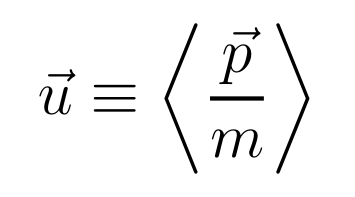

```mathematica
MaTeX["\\vec{u} \\equiv\\left\\langle\\frac{\\vec{p}}{m}\\right\\rangle", Magnification -> 4]
```

```mathematica
ToExpression[StringReplace["\\vec{u} \\equiv\\left\\langle\\frac{\\vec{p}}{m}\\right\\rangle",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

u⃗≡⟨(p⃗)/m⟩

```mathematica
(32) -- The change in how many particles are in a specific area over time is caused by particles moving around. We call this movement of particles a "particle current." It's represented by the symbol Jn, which equals the number of particles (n) multiplied by their velocity (u). 

This idea helps us understand how particles flow and distribute themselves in a system, which is crucial in thermodynamics and statistical mechanics.
```

## (b) Momentum:

```mathematica
(33) -- Let's talk about momentum in collisions. When two objects collide, their total momentum stays the same. This is really important! We can use any straight-line function of momentum (which we write as p with an arrow on top) to show this. In our studies, we'll look at what happens because of this conservation of momentum. It helps us understand how objects behave before and after they bump into each other.
```

Statistical Mechanics
Ramirez (34)

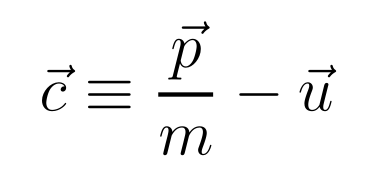

```mathematica
MaTeX["\\vec{c} \\equiv \\frac{\\vec{p}}{m}-\\vec{u}", Magnification -> 4]
```

```mathematica
ToExpression[StringReplace["\\vec{c} \\equiv \\frac{\\vec{p}}{m}-\\vec{u}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

c⃗≡(p⃗)/m-u⃗

(35) -- Substituting $c_{\alpha}$ into eq.(III.79) leads to

Statistical Mechanics
Ramirez (36)

```mathematica
MaTeX["\\partial_{\\beta}\\left(n\\left\\langle\\left(u_{\\beta}+c_{\\beta}\\right) c_{\\alpha}\\right\\rangle\\right)+n \\partial_{t} u_{\\alpha}+n \\partial_{\\beta} u_{\\alpha}\\left\\langle u_{\\beta}+c_{\\beta}\\right\\rangle-n \\frac{F_{\\alpha}}{m}=0", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\partial_{\\beta}\\left(n\\left\\langle\\left(u_{\\beta}+c_{\\beta}\\right) c_{\\alpha}\\right\\rangle\\right)+n \\partial_{t} u_{\\alpha}+n \\partial_{\\beta} u_{\\alpha}\\left\\langle u_{\\beta}+c_{\\beta}\\right\\rangle-n \\frac{F_{\\alpha}}{m}=0",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

∂_β (n ⟨(u_β+c_β) c_α⟩)+n ∂_t u_α+n ∂_β u_α ⟨u_β+c_β⟩-(n F_α)/m==0

(37) -- Let's simplify this concept for better understanding. We know that the average value of cα is zero. This is a useful property that we can apply to our equations (III.81) and (III.82). By doing so, we can simplify these equations and extract more meaningful information about our system. This approach helps us to focus on the most important aspects of the problem and often leads to clearer insights into the thermodynamic behavior we're studying.

Statistical Mechanics
Ramirez (38)

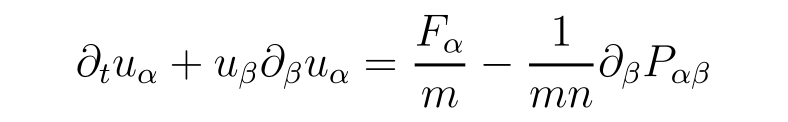

```mathematica
MaTeX["\\partial_{t} u_{\\alpha}+u_{\\beta} \\partial_{\\beta} u_{\\alpha}=\\frac{F_{\\alpha}}{m}-\\frac{1}{m n} \\partial_{\\beta} P_{\\alpha \\beta}", Magnification -> 4]
```

```mathematica
ToExpression[StringReplace["\\partial_{t} u_{\\alpha}+u_{\\beta} \\partial_{\\beta} u_{\\alpha}=\\frac{F_{\\alpha}}{m}-\\frac{1}{m n} \\partial_{\\beta} P_{\\alpha \\beta}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

∂_t u_α+u_β ∂_β u_α==F_α/m-(∂_β P_αβ)/mn

(39) -- In our study of thermodynamics, we now encounter the pressure tensor. This important concept generalizes the familiar scalar pressure to a more comprehensive description of stress in a system. The pressure tensor, denoted as P, is a 3x3 matrix that captures the directional nature of pressure in three-dimensional space. Each element Pij represents the force per unit area acting on a surface perpendicular to the i-axis in the j-direction. This tensor allows us to describe complex stress states in fluids and solids, providing a fuller picture of how forces are distributed within a system. Understanding the pressure tensor is crucial for analyzing advanced thermodynamic systems and their behavior under various conditions.

Statistical Mechanics
Ramirez (40)

```mathematica
MaTeX["P_{\\alpha \\beta} \\equiv m n\\left\\langle c_{\\alpha} c_{\\beta}\\right\\rangle", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["P_{\\alpha \\beta} \\equiv m n\\left\\langle c_{\\alpha} c_{\\beta}\\right\\rangle",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

P_αβ≡m n ⟨c_α c_β⟩

(41) -- Let's break down Newton's equation for fluid motion in a simple way:

When we look at a tiny part of a fluid, it moves according to Newton's second law: force equals mass times acceleration. In our case, we write this as du/dt = Fnet/m, where u is the fluid's velocity.

Now, what makes up this net force? It's not just external forces like gravity. In fluids, we also have to consider how pressure changes from one point to another. These pressure differences push the fluid around, adding an extra force to our equation.

So, when we study fluid motion, we're really looking at how acceleration results from both external forces and internal pressure variations. This gives us a more complete picture of how fluids behave.

## (c) Kinetic energy:

```mathematica
(42) -- Let's talk about kinetic energy in a simple way. Imagine we're looking at a tiny part of a system, like a small group of particles. These particles are always moving around, bumping into each other. The energy they have because of this motion is what we call kinetic energy.

Now, we want to find out the average kinetic energy for this small group. We do this by adding up all the individual kinetic energies and then dividing by the number of particles. This gives us a good idea of how much energy is typically associated with the motion in that specific area.

We can write this average kinetic energy as ε̄ᵏⁱⁿ. It's important because it helps us understand how energetic the particles are in different parts of our system.
```

Statistical Mechanics
Ramirez (43)

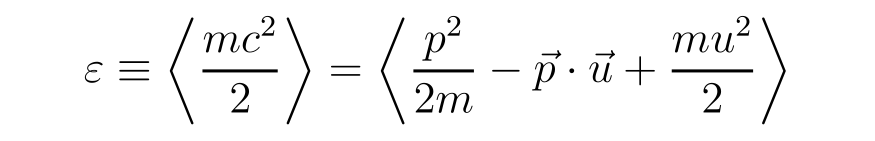

```mathematica
MaTeX["\\varepsilon \\equiv\\left\\langle\\frac{m c^{2}}{2}\\right\\rangle=\\left\\langle\\frac{p^{2}}{2 m}-\\vec{p} \\cdot \\vec{u}+\\frac{m u^{2}}{2}\\right\\rangle", Magnification -> 4]
```

```mathematica
ToExpression[StringReplace["\\varepsilon \\equiv\\left\\langle\\frac{m c^{2}}{2}\\right\\rangle=\\left\\langle\\frac{p^{2}}{2 m}-\\vec{p} \\cdot \\vec{u}+\\frac{m u^{2}}{2}\\right\\rangle",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

(ϵ≡⟨(m c^2)/2⟩)==⟨p^2/(2 m)-p⃗·u⃗+(m u^2)/2⟩

```mathematica
(44) -- Let's look at what happens when we set χ equal to mc.b2/2 in our conservation law equation. Remember, for space and time derivatives, we can write:

∂ε = mcβ∂cβ = -mcβ∂uβ

This relationship helps us understand how energy changes with respect to velocity in our system. By applying this to our conservation law, we can gain insights into the behavior of particles in thermodynamic systems, particularly how their energy and momentum are conserved as they move and interact.
```

```mathematica
MaTeX["\\partial_{t}(n \\varepsilon)+\\partial_{\\alpha}\\left(n\\left\\langle\\left(u_{\\alpha}+c_{\\alpha}\\right) \\frac{m c^{2}}{2}\\right\\rangle\\right)+n m \\partial_{t} u_{\\beta}\\left\\langle c_{\\beta}\\right\\rangle+n m \\partial_{\\alpha} u_{\\beta}\\left\langle\left(u_{\\alpha}+c_{\\alpha}\\right) c_{\\beta}\\right\\rangle-n F_{\\alpha}\left\\langle c_{\\alpha}\\right\\rangle=0", Magnification->2]
```

-Graphics-

```mathematica
(45) -- Let's break down this complex equation into simpler terms. We're looking at how energy changes in a system of particles over time. Imagine a group of tiny balls bouncing around in a box. The equation describes how their energy changes as they move and interact.

The first part, ∂t(nε), tells us how the total energy of all the particles changes over time. The next part, with the ∂α, shows how energy flows from one place to another due to the particles' motion.

The remaining terms describe how the particles' energy is affected by forces acting on them and how they collide with each other. These factors can cause the particles to speed up, slow down, or change direction.

In essence, this equation helps us understand how energy moves and transforms within a system of many particles, which is crucial for studying thermodynamics and statistical mechanics.
```

```mathematica
(46) -- Let's simplify this equation by using a helpful property: the average value of cα is zero. This means we can remove some terms from our equation, making it easier to work with. By doing this, we're focusing on the most important parts of the equation without losing its physical meaning. Remember, in thermodynamics and statistical mechanics, we often use averages to describe the behavior of large systems, and this simplification is a common technique to make our calculations more manageable.
```

Statistical Mechanics
Ramirez (47)

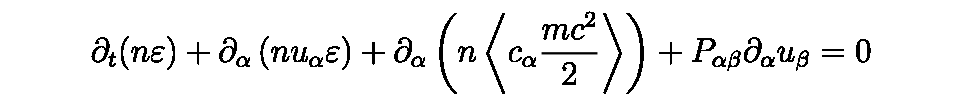

```mathematica
MaTeX["\\partial_{t}(n \\varepsilon)+\\partial_{\\alpha}\\left(n u_{\\alpha} \\varepsilon\\right)+\\partial_{\\alpha}\\left(n\\left\\langle c_{\\alpha} \\frac{m c^{2}}{2}\\right\\rangle\\right)+P_{\\alpha \\beta} \\partial_{\\alpha} u_{\\beta}=0", Magnification -> 4]
```

```mathematica
ToExpression[StringReplace["\\partial_{t}(n \\varepsilon)+\\partial_{\\alpha}\\left(n u_{\\alpha} \\varepsilon\\right)+\\partial_{\\alpha}\\left(n\\left\\langle c_{\\alpha} \\frac{m c^{2}}{2}\\right\\rangle\\right)+P_{\\alpha \\beta} \\partial_{\\alpha} u_{\\beta}=0",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

∂_t (n ϵ)+∂_α (n u_α ϵ)+∂_α (n ⟨1/2 c_α (m c^2)⟩)+P_αβ ∂_α u_β==0

(48) -- We next take out the dependence on $n$ in the first two terms of the above equation, finding

Statistical Mechanics
Ramirez (49)

```mathematica
MaTeX["\\varepsilon \\partial_{t} n+n \\partial_{t} \\varepsilon+\\varepsilon \\partial_{\\alpha}\\left(n u_{\\alpha}\\right)+n u_{\\alpha} \\partial_{\\alpha} \\varepsilon+\\partial_{\\alpha} h_{\\alpha}+P_{\\alpha \\beta} u_{\\alpha \\beta}=0", Magnification -> 4]
```

-Graphics-

```mathematica
ToExpression[StringReplace["\\varepsilon \\partial_{t} n+n \\partial_{t} \\varepsilon+\\varepsilon \\partial_{\\alpha}\\left(n u_{\\alpha}\\right)+n u_{\\alpha} \\partial_{\\alpha} \\varepsilon+\\partial_{\\alpha} h_{\\alpha}+P_{\\alpha \\beta} u_{\\alpha \\beta}=0",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

ϵ ∂_t n+n ∂_t ϵ+ϵ ∂_α (n u_α)+n u_α ∂_α ϵ+∂_α h_α+P_αβ u_αβ==0

```mathematica
(50) -- where we have also introduced the local heat flux
```

Statistical Mechanics
Ramirez (51)

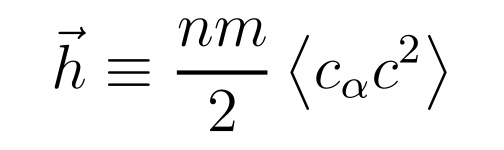

```mathematica
MaTeX["\\vec{h} \\equiv \\frac{n m}{2}\\left\\langle c_{\\alpha} c^{2}\\right\\rangle", Magnification -> 4]
```

```mathematica
ToExpression[StringReplace["\\vec{h} \\equiv \\frac{n m}{2}\\left\\langle c_{\\alpha} c^{2}\\right\\rangle",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

h⃗≡1/2 nm ⟨c_α c^2⟩

(52) -- and the rate of strain tensor

Statistical Mechanics
Ramirez (53)

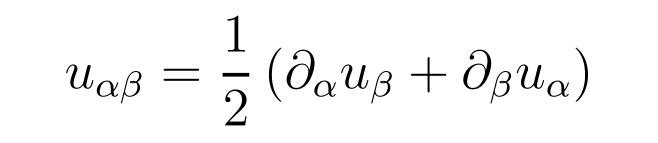

```mathematica
MaTeX["u_{\\alpha \\beta}=\\frac{1}{2}\\left(\\partial_{\\alpha} u_{\\beta}+\\partial_{\\beta} u_{\\alpha}\\right)", Magnification -> 4]
```

```mathematica
ToExpression[StringReplace["u_{\\alpha \\beta}=\\frac{1}{2}\\left(\\partial_{\\alpha} u_{\\beta}+\\partial_{\\beta} u_{\\alpha}\\right)",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

u_αβ==1/2 (∂_α u_β+∂_β u_α)

(54) -- Let's simplify this a bit. We're working with two equations here, and we want to make things easier to understand. By using equation (III.80), we can get rid of some parts in equation (III.89). Specifically, we're removing the first and third terms from (III.89). This helps us focus on the most important parts of the equation and makes our calculations simpler. Think of it like cleaning up a messy room - we're removing the unnecessary items to see what's really important. This process is common in thermodynamics when we're trying to understand complex systems more easily.

Statistical Mechanics
Ramirez (55)

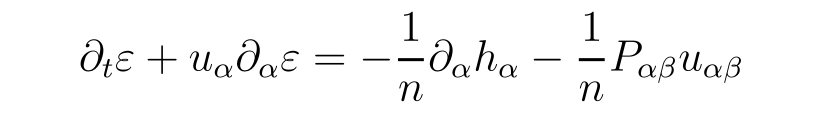

```mathematica
MaTeX["\\partial_{t} \\varepsilon+u_{\\alpha} \\partial_{\\alpha} \\varepsilon=-\\frac{1}{n} \\partial_{\\alpha} h_{\\alpha}-\\frac{1}{n} P_{\\alpha \\beta} u_{\\alpha \\beta}", Magnification -> 4]
```

```mathematica
ToExpression[StringReplace["\\partial_{t} \\varepsilon+u_{\\alpha} \\partial_{\\alpha} \\varepsilon=-\\frac{1}{n} \\partial_{\\alpha} h_{\\alpha}-\\frac{1}{n} P_{\\alpha \\beta} u_{\\alpha \\beta}",{"const."->"C","\\perp"->"\\perpendicular", "\\times"->"x", "~"->""}],TeXForm,HoldForm]
```

∂_t ϵ+u_α ∂_α ϵ==-(∂_α h_α)/n-(P_αβ u_αβ)/n

```mathematica
(56) -- To solve the equations that describe how fluids move, we need to know a few key things. These are the number of particles (n), their speed and direction (u), and their energy (ε). But to fully understand what's happening, we also need to know about the pressure (Pαβ) and heat flow (h) in the fluid.

We can figure out the pressure and heat flow in two ways:
1. By using general rules based on what we observe in experiments
2. By calculating them from a more detailed description of how the particles are distributed (f1)

In the next parts of this book, we'll look at both these methods to get a complete picture of fluid behavior.
```

## Reference

https://assets.cambridge.org/97805218/73420/frontmatter/9780521873420_frontmatter.pdf

```mathematica
mathPiXDB1="VarsPaper23_v1.mx";
DumpSave[$WorkDir<>"mathPiXDB/"<>mathPiXDB1,"Global`"];
```

◀ prev - + prox ▶

e Guardar
d Resetear